```mathematica
PacletDir="/Users/cookgb/Research/PublicPaclets/HDF5KerrModes";
```

```mathematica
PacletDir="/home/cookgb/Research/PublicPaclets/HDF5KerrModes";
```

```mathematica
PacletDirectoryLoad[PacletDir]
```

{/home/cookgb/Research/PublicPaclets/HDF5KerrModes}

```mathematica
Needs["PacletTools`"]
```

```mathematica
PacletBuild[PacletDir<>"/HDF5KerrModes"];
```

```mathematica
Needs["HDF5KerrModes`"]
```

```mathematica
HDF5KerrModesDir["/home/cookgb/Research/KerrQNM/KerrModes/QNMData/PhasedQNM/HDF5/"]
```

/home/cookgb/Research/KerrQNM/KerrModes/QNMData/PhasedQNM/HDF5/

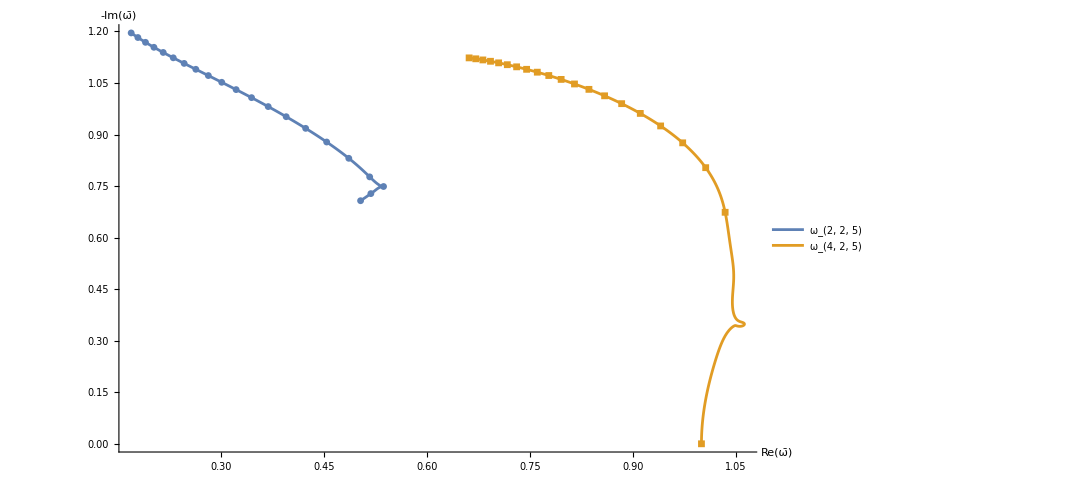

```mathematica
QNMPlotω[{{2,2,5},{4,2,5}},PlotLegends->Placed[Style[#,16,Black]&/@{"ω_(2, 2, 5)","ω_(4, 2, 5)"},{Right,Top}]]
```

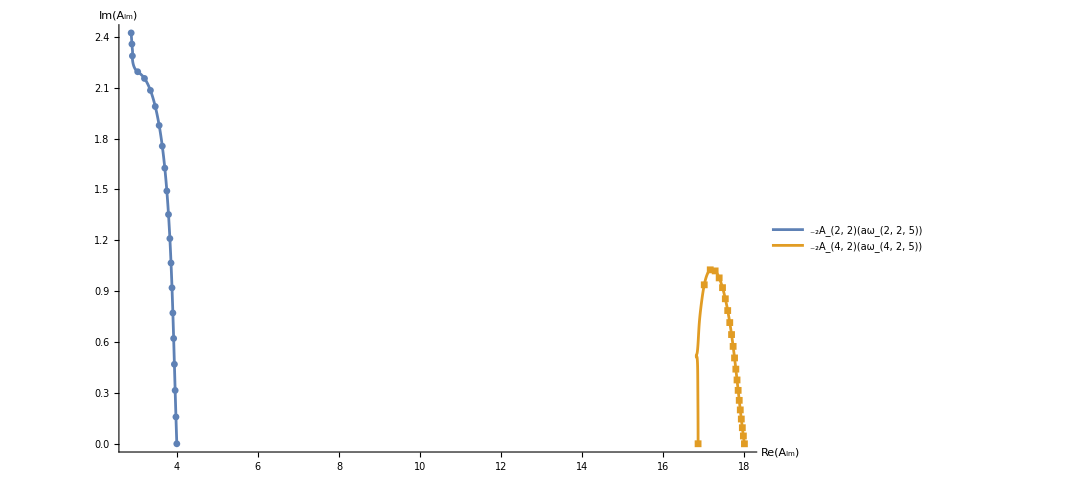

```mathematica
QNMPlotAlm[{{2,2,5},{4,2,5}},PlotLegends->Placed[Style[#,16,Black]&/@{"_-2A_(2, 2)(aω_(2, 2, 5))","_-2A_(4, 2)(aω_(4, 2, 5))"},{Right,Top}]]
```

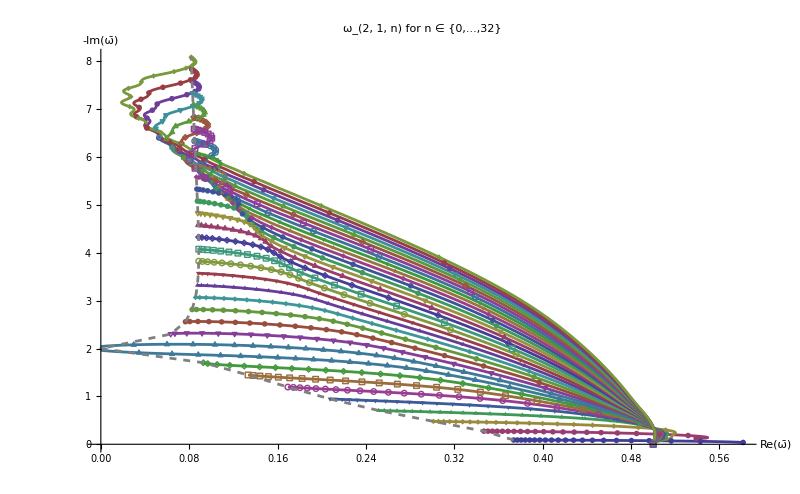

```mathematica
QNMPlotAllωTones[1,Range[2,2],OvertoneList->Range[0,32],PlotLabel->Style["ω_(2, 1, n) for n ∈ {0,...,32}",16,Black]]
```

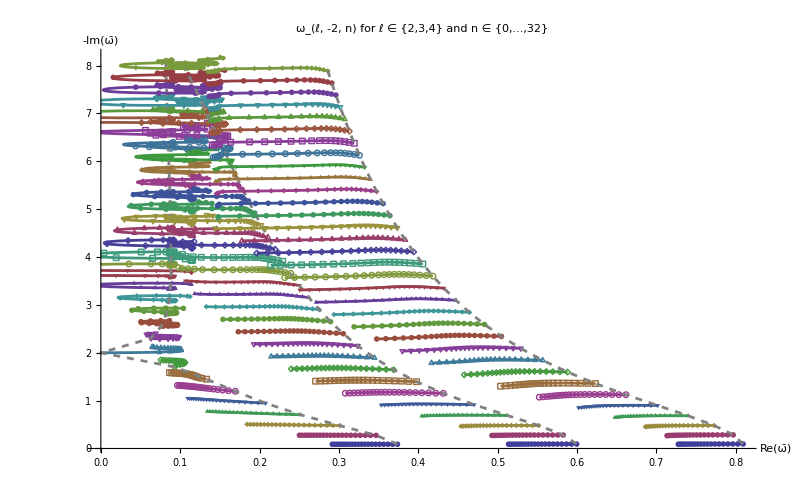

```mathematica
QNMPlotAllωTones[-2,Range[2,4],OvertoneList->Range[0,32],PlotLabel->Style["ω_(ℓ, -2, n) for ℓ ∈ {2,3,4} and n ∈ {0,...,32}",16,Black]]
```

```mathematica
plots1=PlotQNMSWSF[2,2,0,{1,-1,50},PlotPoints->100,PhaseChoice->"SL-C",ImageSize->Large,PlotLabel->Style["_-2S_(2, 2)(x; aω_(2, 2, 0)) : 𝒫_(SL - C)",16,Black],LabelStyle->Directive[14,Black],Epilog->{Inset[Hold[Style["ā="<>ToString[DecimalForm[#[[2]],{11,10}]],14]],{-0.513,0.8}],Inset[Hold[Style["c="<>ToString[DecimalForm[Re[#[[2]]#[[3]]],{5,4}]]<>ToString[DecimalForm[Im[#[[2]]#[[3]]],{5,4}]]<>"ⅈ",14]],{-0.5,0.68}]}];
```

```mathematica
ListAnimate[plots1]
```

```mathematica
plots1cz=PlotQNMSWSF[2,2,0,{1,-1,50},PlotPoints->100,PhaseChoice->"CZ-SL",ImageSize->Large,PlotLabel->Style["_-2S_(2, 2)(x; aω_(2, 2, 0)) : 𝒫_(CZ - SL)",16,Black],LabelStyle->Directive[14,Black],Epilog->{Inset[Hold[Style["ā="<>ToString[DecimalForm[#[[2]],{11,10}]],14]],{-0.513,0.8}],Inset[Hold[Style["c="<>ToString[DecimalForm[Re[#[[2]]#[[3]]],{5,4}]]<>ToString[DecimalForm[Im[#[[2]]#[[3]]],{5,4}]]<>"ⅈ",14]],{-0.5,0.68}]}];
```

```mathematica
ListAnimate[plots1cz]
```

```mathematica
plots2=PlotQNMSWSF[3,0,3,{1,-1,50},PlotPoints->100,PhaseChoice->"SL-C",ImageSize->Large,PlotLabel->Style["_-2S_(3, 0)(x; aω_(3, 0, 3)) : 𝒫_(SL - C)",16,Black],LabelStyle->Directive[14,Black],Epilog->{Inset[Hold[Style["ā="<>ToString[DecimalForm[#[[2]],{11,10}]],14]],{-0.513,0.8}],Inset[Hold[Style["c="<>ToString[DecimalForm[Re[#[[2]]#[[3]]],{5,4}]]<>ToString[DecimalForm[Im[#[[2]]#[[3]]],{5,4}]]<>"ⅈ",14]],{-0.5,0.68}]}];
```

```mathematica
ListAnimate[plots2]
```

```mathematica
plots2cz=PlotQNMSWSF[3,0,3,{1,-1,50},PlotPoints->100,PhaseChoice->"CZ-SL",ImageSize->Large,PlotLabel->Style["_-2S_(3, 0)(x; aω_(3, 0, 3)) : 𝒫_(CZ - SL)",16,Black],LabelStyle->Directive[14,Black],Epilog->{Inset[Hold[Style["ā="<>ToString[DecimalForm[#[[2]],{11,10}]],14]],{-0.513,0.8}],Inset[Hold[Style["c="<>ToString[DecimalForm[Re[#[[2]]#[[3]]],{5,4}]]<>ToString[DecimalForm[Im[#[[2]]#[[3]]],{5,4}]]<>"ⅈ",14]],{-0.5,0.68}]}];
```

```mathematica
ListAnimate[plots2cz]
```

```mathematica
plots3=PlotQNMSWSF[8,-6,3,{1,-1,50},PlotPoints->100,PhaseChoice->"SL-C",ImageSize->Large,PlotLabel->Style["_-2S_(8, -6)(x; aω_(8, -6, 3)) : 𝒫_(SL - C)",16,Black],LabelStyle->Directive[14,Black],Epilog->{Inset[Hold[Style["ā="<>ToString[DecimalForm[#[[2]],{11,10}]],14]],{0.5,-0.28}],Inset[Hold[Style["c="<>ToString[DecimalForm[Re[#[[2]]#[[3]]],{5,4}]]<>ToString[DecimalForm[Im[#[[2]]#[[3]]],{5,4}]]<>"ⅈ",14]],{0.513,-0.4}]}];
```

```mathematica
ListAnimate[plots3]
```

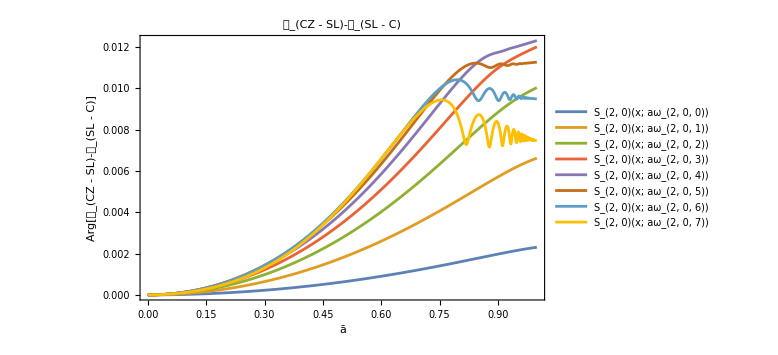

```mathematica
ListLinePlot[{Transpose[{#[[3]],Arg[#[[1]]]}&[PhaseDifferenceQNM[2,0,0,PhaseChoice->"CZ-SL"]]],Transpose[{#[[3]],Arg[#[[1]]]}&[PhaseDifferenceQNM[2,0,1,PhaseChoice->"CZ-SL"]]],Transpose[{#[[3]],Arg[#[[1]]]}&[PhaseDifferenceQNM[2,0,2,PhaseChoice->"CZ-SL"]]],Transpose[{#[[3]],Arg[#[[1]]]}&[PhaseDifferenceQNM[2,0,3,PhaseChoice->"CZ-SL"]]],Transpose[{#[[3]],Arg[#[[1]]]}&[PhaseDifferenceQNM[2,0,4,PhaseChoice->"CZ-SL"]]],Transpose[{#[[3]],Arg[#[[1]]]}&[PhaseDifferenceQNM[2,0,5,PhaseChoice->"CZ-SL"]]],Transpose[{#[[3]],Arg[#[[1]]]}&[PhaseDifferenceQNM[2,0,6,PhaseChoice->"CZ-SL"]]],Transpose[{#[[3]],Arg[#[[1]]]}&[PhaseDifferenceQNM[2,0,7,PhaseChoice->"CZ-SL"]]]},PlotRange->All,ImageSize->Large,PlotLabel->Style["𝒫_(CZ - SL)-𝒫_(SL - C)",16,Black],PlotLegends->Placed[Style[#,12,Black]&/@{"S_(2, 0)(x; aω_(2, 0, 0))","S_(2, 0)(x; aω_(2, 0, 1))","S_(2, 0)(x; aω_(2, 0, 2))","S_(2, 0)(x; aω_(2, 0, 3))","S_(2, 0)(x; aω_(2, 0, 4))","S_(2, 0)(x; aω_(2, 0, 5))","S_(2, 0)(x; aω_(2, 0, 6))","S_(2, 0)(x; aω_(2, 0, 7))"},{Left,Top}],Frame->{{True,False},{True,False}},FrameLabel->{"ā","Arg[𝒫_(CZ - SL)-𝒫_(SL - C)]"},LabelStyle->Directive[14,Black]]
```

```mathematica
QNMSpectralCoef[12,2,5,Loga->True]
```

-Graphics3D-

```mathematica
QNMSpectralCoefRe[12,2,5,Loga->True,PlotRange->Automatic]
```

-Graphics3D-

```mathematica
QNMSpectralCoefIm[12,2,5,Loga->True]
```

-Graphics3D-

```mathematica
HDF5KerrModesDir["/home/cookgb/Research/KerrQNM/KerrModes/TTMData/HDF5/"]
```

/home/cookgb/Research/KerrQNM/KerrModes/TTMData/HDF5/

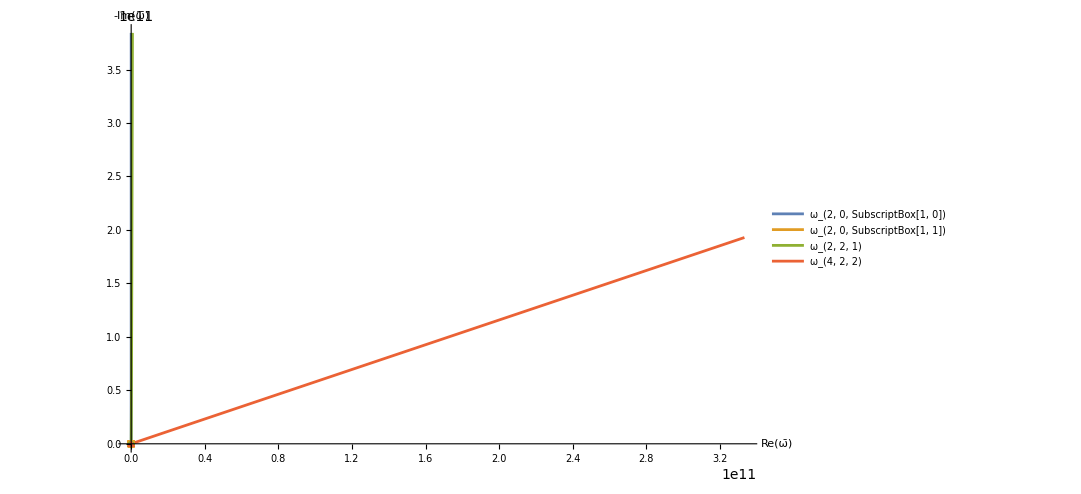

```mathematica
TTMRPlotω[{{2,0,{1,0}},{2,0,{1,1}},{2,2,1},{4,2,2}},PlotLegends->Placed[Style[#,16,Black]&/@{"ω_(2, 0, SubscriptBox[1, 0])","ω_(2, 0, SubscriptBox[1, 1])","ω_(2, 2, 1)","ω_(4, 2, 2)"},{Right,Top}]]
```

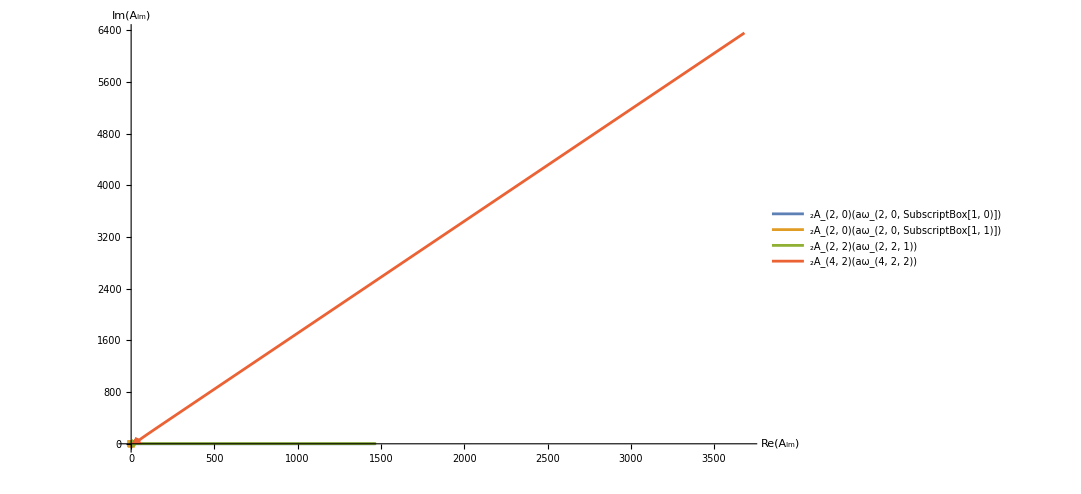

```mathematica
TTMRPlotAlm[{{2,0,{1,0}},{2,0,{1,1}},{2,2,1},{4,2,2}},PlotLegends->Placed[Style[#,16,Black]&/@{"_2A_(2, 0)(aω_(2, 0, SubscriptBox[1, 0)])","_2A_(2, 0)(aω_(2, 0, SubscriptBox[1, 1)])","_2A_(2, 2)(aω_(2, 2, 1))","_2A_(4, 2)(aω_(4, 2, 2))"},{0.2,0.8}]]
```

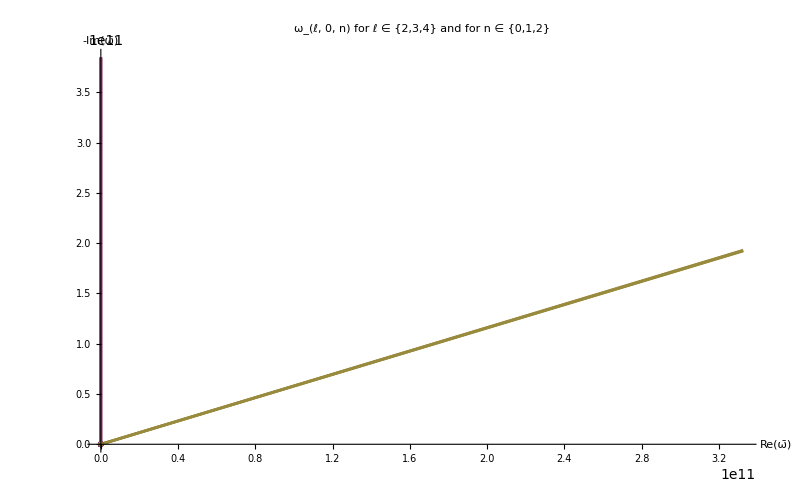

```mathematica
TTMRPlotAllωTones[0,Range[2,4],OvertoneList->Range[0,2],PlotLabel->Style["ω_(ℓ, 0, n) for ℓ ∈ {2,3,4} and for n ∈ {0,1,2}",16,Black]]
```

```mathematica
plots4=PlotTTMSWSF["R",2,2,0,{1,-1,50},PlotPoints->100,PhaseChoice->"SL-C",ImageSize->Large,PlotLabel->Style["_2S_(2, 2)(x; aω_(2, 2, 0)) : 𝒫_(SL - C)",16,Black],LabelStyle->Directive[14,Black],Epilog->{Inset[Hold[Style["ā="<>ToString[DecimalForm[#[[2]],{11,10}]],14]],{0.5,0.8}],Inset[Hold[Style["c="<>ToString[DecimalForm[Re[#[[2]]#[[3]]],{5,4}]]<>ToString[DecimalForm[Im[#[[2]]#[[3]]],{5,4}]]<>"ⅈ",14]],{0.513,0.68}]}];
```

```mathematica
ListAnimate[plots4]
```

```mathematica
plots4cz=PlotTTMSWSF["R",2,2,0,{1,-1,50},PlotPoints->100,PhaseChoice->"CZ-SL",ImageSize->Large,PlotLabel->Style["_2S_(2, 2)(x; aω_(2, 2, 0)) : 𝒫_(CZ - SL)",16,Black],LabelStyle->Directive[14,Black],Epilog->{Inset[Hold[Style["ā="<>ToString[DecimalForm[#[[2]],{11,10}]],14]],{0.5,0.8}],Inset[Hold[Style["c="<>ToString[DecimalForm[Re[#[[2]]#[[3]]],{5,4}]]<>ToString[DecimalForm[Im[#[[2]]#[[3]]],{5,4}]]<>"ⅈ",14]],{0.513,0.68}]}];
```

```mathematica
ListAnimate[plots4cz]
```

```mathematica
plots5a=PlotTTMSWSF["R",2,2,2,{1,30,2},PlotPoints->400,PhaseChoice->"SL-C",ImageSize->Large,PlotRange->{{-1,1},{-2,4}},PlotLabel->Style["_2S_(2, 2)(x; aω_(2, 2, 2)) : 𝒫_(SL - C)",16,Black],LabelStyle->Directive[14,Black],Epilog->{Inset[Hold[Style["ā="<>ToString[DecimalForm[#[[2]],{11,10}]],14]],{0.5,1.6}],Inset[Hold[Style["c="<>ToString[DecimalForm[Re[#[[2]]#[[3]]],{5,2}]]<>ToString[DecimalForm[Im[#[[2]]#[[3]]],{5,2}]]<>"ⅈ",14]],{0.513,1.25}]}];
```

```mathematica
plots5b=PlotTTMSWSF["R",2,2,2,{32,-1,50},PlotPoints->100,PhaseChoice->"SL-C",ImageSize->Large,PlotRange->{{-1,1},{-2,4}},PlotLabel->Style["_2S_(2, 2)(x; aω_(2, 2, 2)) : 𝒫_(SL - C)",16,Black],LabelStyle->Directive[14,Black],Epilog->{Inset[Hold[Style["ā="<>ToString[DecimalForm[#[[2]],{11,10}]],14]],{0.5,1.6}],Inset[Hold[Style["c="<>ToString[DecimalForm[Re[#[[2]]#[[3]]],{5,4}]]<>ToString[DecimalForm[Im[#[[2]]#[[3]]],{5,4}]]<>"ⅈ",14]],{0.513,1.25}]}];
```

```mathematica
ListAnimate[Join[plots5a,plots5b]]
```

```mathematica
plots6a=PlotTTMSWSF["R",8,0,{1,0},{1,79,3},PlotPoints->200,PhaseChoice->"SL-C",ImageSize->Large,PlotRange->{{-1,1},{-2.7,3.5}},PlotLabel->Style["_2S_(8, 0)(x; aω_(8, 0, SubscriptBox[1, 0])) : 𝒫_(SL - C)",16,Black],LabelStyle->Directive[14,Black],Epilog->{Inset[Hold[Style["ā="<>ToString[DecimalForm[#[[2]],{11,10}]],14]],{0.5,1.6}],Inset[Hold[Style["c="<>ToString[DecimalForm[Re[#[[2]]#[[3]]],{5,4}]]<>ToString[DecimalForm[Im[#[[2]]#[[3]]],{5,2}]]<>"ⅈ",14]],{0.513,1.25}]}];
```

```mathematica
plots6b=PlotTTMSWSF["R",8,0,{1,0},{82,-1,20},PlotPoints->100,PhaseChoice->"SL-C",ImageSize->Large,PlotRange->{{-1,1},{-2.7,3.5}},PlotLabel->Style["_2S_(8, 0)(x; aω_(8, 0, SubscriptBox[1, 0])) : 𝒫_(SL - C)",16,Black],LabelStyle->Directive[14,Black],Epilog->{Inset[Hold[Style["ā="<>ToString[DecimalForm[#[[2]],{11,10}]],14]],{0.5,1.6}],Inset[Hold[Style["c="<>ToString[DecimalForm[Re[#[[2]]#[[3]]],{5,4}]]<>ToString[DecimalForm[Im[#[[2]]#[[3]]],{5,3}]]<>"ⅈ",14]],{0.513,1.25}]}];
```

```mathematica
ListAnimate[Join[plots6a,plots6b]]
```

```mathematica
plots7a=PlotTTMSWSF["R",8,0,{1,0},{1,79,3},PlotPoints->200,PhaseChoice->"CZ-SL",ImageSize->Large,PlotRange->{{-1,1},{-3.5,2.7}},PlotLabel->Style["_2S_(8, 0)(x; aω_(8, 0, SubscriptBox[1, 0])) : 𝒫_(CZ - SL)",16,Black],LabelStyle->Directive[14,Black],Epilog->{Inset[Hold[Style["ā="<>ToString[DecimalForm[#[[2]],{11,10}]],14]],{0.5,1.6}],Inset[Hold[Style["c="<>ToString[DecimalForm[Re[#[[2]]#[[3]]],{5,4}]]<>ToString[DecimalForm[Im[#[[2]]#[[3]]],{5,2}]]<>"ⅈ",14]],{0.513,1.25}]}];
```

```mathematica
plots7b=PlotTTMSWSF["R",8,0,{1,0},{82,-1,20},PlotPoints->100,PhaseChoice->"CZ-SL",ImageSize->Large,PlotRange->{{-1,1},{-3.5,2.7}},PlotLabel->Style["_2S_(8, 0)(x; aω_(8, 0, SubscriptBox[1, 0])) : 𝒫_(CZ - SL)",16,Black],LabelStyle->Directive[14,Black],Epilog->{Inset[Hold[Style["ā="<>ToString[DecimalForm[#[[2]],{11,10}]],14]],{0.5,1.6}],Inset[Hold[Style["c="<>ToString[DecimalForm[Re[#[[2]]#[[3]]],{5,4}]]<>ToString[DecimalForm[Im[#[[2]]#[[3]]],{5,3}]]<>"ⅈ",14]],{0.513,1.25}]}];
```

```mathematica
ListAnimate[Join[plots7a,plots7b]]
```

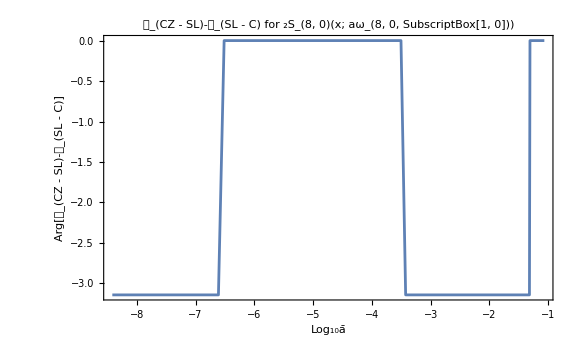

```mathematica
ListLinePlot[Transpose[{Log10[#[[3]]],Arg[#[[1]]]}&[PhaseDifferenceTTM["R",8,0,{1,0},PhaseChoice->"CZ-SL"]]],PlotRange->All,ImageSize->Large,PlotLabel->Style["𝒫_(CZ - SL)-𝒫_(SL - C)  for  _2S_(8, 0)(x; aω_(8, 0, SubscriptBox[1, 0]))",16,Black],Frame->{{True,False},{True,False}},FrameLabel->{"Log_10ā","Arg[𝒫_(CZ - SL)-𝒫_(SL - C)]"},LabelStyle->Directive[14,Black]]
```